# 三角形的面积

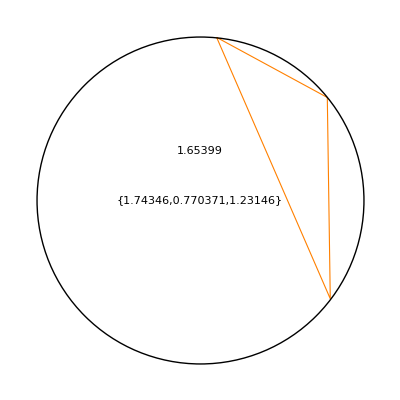

```mathematica
With[{pts=RandomPoint[Circle[],3]},abc=EuclideanDistance@@#&/@Subsets[pts,{2}];Graphics[{{EdgeForm[{Orange}],FaceForm[ ],Triangle[pts]},CircleThrough[pts],Text[abc],Text[Times@@abc,{0,0.3}]}]]
```

### 使用海伦公式来计算三角形面积

```mathematica
FormulaLookup["heron's formula"]
```

{TriangleAreaSSS}

```mathematica
FormulaData["TriangleAreaSSS"]
```

{s Length==1/2 (a Length+b Length+c Length),A Area==√(s Length (-a Length+s Length) (-b Length+s Length) (-c Length+s Length))}

```mathematica
FormulaData["TriangleAreaSSS","Association"]
```

<|s Length→1/2 (a Length+b Length+c Length),A Area→√(s Length (-a Length+s Length) (-b Length+s Length) (-c Length+s Length))|>

```mathematica
FormulaData["TriangleAreaSSS","QuantityVariableTable"]
```

symbol | description | physical quantity | dimensions
s | semiperimeter | Length | {LengthUnit,1}
a | first side length | Length | {LengthUnit,1}
b | second side length | Length | {LengthUnit,1}
c | third side length | Length | {LengthUnit,1}
A | area | Area | {LengthUnit,2}

```mathematica
FormulaData["TriangleAreaSSS",{"a"->abc[[1]],"b"->abc[[2]],"c"->abc[[3]]}]
```

s Length==1.87264&&A Area==0.413497

```mathematica
Solve["s" "Length"==1.8726446165754909&&"A" "Area"==0.4134965173621506]
```

{{A Area→0.413497,s Length→1.87264}}

```mathematica
First[{{"A" "Area"->0.4134965173621506,"s" "Length"->1.8726446165754909}}]
```

{A Area→0.413497,s Length→1.87264}

```mathematica
{"A" "Area"->0.4134965173621506,"s" "Length"->1.8726446165754909}/.Rule->List
```

{{A Area,0.413497},{s Length,1.87264}}

```mathematica
{Times@@abc,4*0.4134965173621506}
```

{1.65399,1.65399}